```mathematica
(* Helper Functions *)
a[params_] := Transpose[{params}] 
listProduct[l_] := Product[l[[i]],{i,1,Length[l]}]
grabElements[l_,e_] := Map[l[[#]]&,e] 
generateFluxCoefficients[GE_,S_] :=Map[listProduct[grabElements[GE,Position[#,_?Positive][[All,1]]]]&,Transpose[S]]
solveForParameters[v_,coeff_]  := MapThread[#1/#2&,{v,coeff}]
solveForFluxes[SS_,fluxes_,S_,x1_,x2_,x3_,error_] := fluxes /.NMinimize[{Norm[SS - S.a[fluxes]],fluxes ≥ 0.001,fluxes[[-3]] ==x1,fluxes[[-2]] ==x2,fluxes[[-1]]==x3},fluxes,AccuracyGoal->4][[2]];
FVA[SS_,fluxes_,S_] := {
Map[NMinimize[
{#,fluxes>=.001 ,Norm[SS-S.a[fluxes]] == 0},fluxes,MaxIterations -> 1000,AccuracyGoal->2]&,fluxes][[All,1]],
Map[NMaximize[
{#,fluxes>=.001 ,Norm[SS-S.a[fluxes]] == 0},fluxes,MaxIterations -> 1000,AccuracyGoal->2]&,fluxes][[All,1]]};
getTermFromReaction[SCol_,species_,rateConstant_,fluxes_] := 
Module[{term=rateConstant},
Map[(term = term *(species[[#]])^Abs[SCol[[#]]])&,Position[SCol,_?Negative][[All,1]]];
If[term == rateConstant,term += rateConstant*fluxes[[Position[SCol,_?Positive][[1,1]]]]];
{Map[{SCol[[#]],species[[#]]}&,Range[Length[SCol]]],
term}
]
addTermToReaction[reactionList_,species_,term_,toReactions_] := 
Module[{temp},
temp = reactionList;
Map[
temp[[Position[species,#[[2]]][[1,1]]]] += #[[1]]*term &,
toReactions];
temp]
generateExpressions[S_,species_,IC_,var_,rateConstants_,fluxes_] := 
Module[{reactionList = ConstantArray[0,Length[species]],allReactions},
allReactions = MapThread[getTermFromReaction[#1,species,#2,fluxes]&,{Transpose[S],rateConstants}];
allReactions = Total[Map[addTermToReaction[reactionList,species,#[[2]],#[[1]]]&,allReactions]];
Join[
MapThread[#2 == #1&,{allReactions /. Map[# -> #[var]&,species],species /. Map[# -> #'[var]&,species]}],
MapThread[#2 == #1&,{IC,species /. Map[# -> #[0]&,species]}]
]
]
```

For the given toy reaction network:
aE->a
b ->a 
a ->b
B -> C + D
D + E -> F
F -> D + E
E + A -> G
A + D -> E
->C (measured)
->G (measured)

```mathematica
(*Reaction Network*)
S = {{0,0,0,0,0,0,0,0,0,-1}{1,-1,0,0,0,1,-1,0,0,1},{-1,1,-1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,-1,0,0},{0,0,1,-1,1,0,-1,0,0,0},{0,0,0,-1,1,-1,1,0,0,0},{0,0,0,1,-1,0,0,0,0,0},{0,0,0,0,0,1,0,0,-1,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,-1}};
MatrixRank[S]
Length[S]
fluxes = {v1,v2,v3,v4,v5,v6,v7,v8,v9,v10};
species = {a,b,c,d,e,f,g,aE,cE,gE};
(species.S)
SS  = ConstantArray[0,{Length[S],1}];
error = .001;
tmax =1000;
bolus = 10;

Print[SS//MatrixForm,"=",S//MatrixForm,a[fluxes] //MatrixForm]
```

8

10

{-s1,s1,-s1+s2+s3,-s3-s4+s5,s3+s4-s5,-s4+s6,-s3+s4,-s2+s7,s3O-s6,-s1O-s7O}

(0
0
0
0
0
0
0
0
0
0)=(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | -1 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10)

```mathematica
(*Find the maximum flux for each reaction individually *)
{fluxMinimum,fluxMaximum} =FVA[SS,fluxes,S]
Print[fluxMinimum // MatrixForm,"≤",a[fluxes] // MatrixForm, "≤" ,fluxMaximum // MatrixForm]
```

7

7

{s1-s2,-s1+s2,-s2+s3+s4,-s4-s5+s6,s4+s5-s6,s1-s5+s7,-s1-s4+s5,-s3,-s7,s1}

10

0.001

(0
0
0
0
0
0
0)=(1 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 1
-1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | -1 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0)(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10)

(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10)=(0.400664
1.40066
1.
0.963101
0.963101
1.
1.
1.
1.
1.)

{11.0287,2.15991,2.69365,0.643577,1.14037,1.69622,165.052}

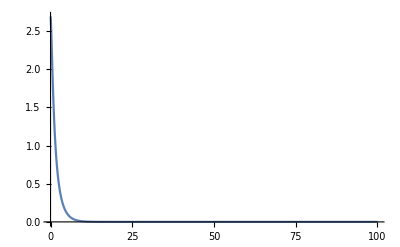
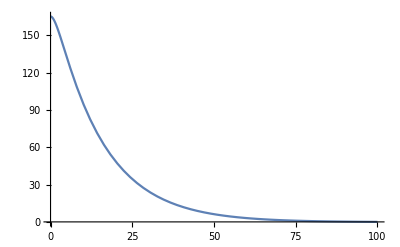

```mathematica
(*Measured flux values for WT*)
x1 = 1;
x2 = 1;
x3 = 1;
 fluxValuesWT = solveForFluxes[SS,fluxes,S,x1,x2,x3,error];
Print[a[fluxes] // MatrixForm,"=",a[fluxValuesWT] //MatrixForm] 
GEWT = RandomReal[{0,1},Length[S]];
fluxCoefficientsWT = solveForParameters[fluxValuesWT,generateFluxCoefficients[GEWT,S]];
baseLineKs = RandomReal[{0,10},Length[fluxValuesWT]];
(*AppendTo[baseLineKs,1];*)
expressions = generateExpressions[S,species,ConstantArray[0,Length[species]],t,baseLineKs,fluxValuesWT];
sol =NDSolve[expressions,species,{t,0,tmax}];
(*Map[Plot[Evaluate[#[t] /. sol],{t,0,1000},PlotRange -> All]&,species]*)
SSConcentrationsWT = Map[(Evaluate[#[tmax] /. sol])[[1]]&,species]
sol =NDSolve[generateExpressions[S[[All,Range[Length[S[[1,All]]]-1]]],species,Join[{bolus},SSConcentrationsWT[[2;;-1]]],t,baseLineKs[[1;;-2]]],species,{t,0,tmax/10}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax/10},PlotRange -> All]&,{s3,s7}]
```

{K}_m/{K}_wt = (3.52947
0.797529
1.16602
3.86934
2.74628
0.199259
1.17301
0.8
0.6
0.947997)

{52.1901,7.94983,1.07453,0.0144247,13.9467,0.046796,1.87353}

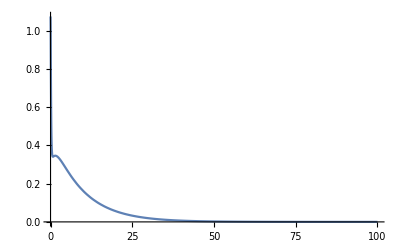
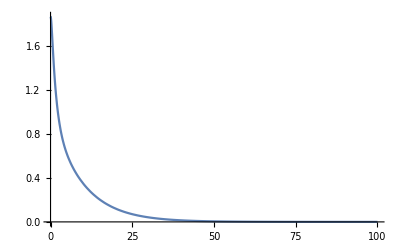

{K}_m/{K}_wt = (0.347976
2.96565
0.058579
0.79541
0.813894
0.0422596
1.21855)

```mathematica
x1 = .8;
x2 = .6;
x3 = 1;
 fluxValuesM = solveForFluxes[SS,fluxes,S,x1,x2,x3,error];
(*Print[a[fluxes] // MatrixForm,"=",a[fluxValuesM] //MatrixForm] *)
GEM = RandomReal[{0,1},Length[S]];
fluxCoefficientsM = solveForParameters[fluxValuesM,generateFluxCoefficients[GEM,S]];
ratioKs = fluxCoefficientsM/fluxCoefficientsWT;
Print["{K}_m/{K}_wt = ", ratioKs// MatrixForm]
expressions = generateExpressions[S,species,ConstantArray[0,Length[species]],t,baseLineKs*ratioKs,fluxValuesM];
sol =NDSolve[expressions,species,{t,0,tmax}];
(*Map[Plot[Evaluate[#[t] /. sol],{t,0,1000},PlotRange -> All]&,species]*)
SSConcentrationsM = Map[(Evaluate[#[tmax] /. sol])[[1]]&,species]
sol =NDSolve[generateExpressions[S[[All,Range[Length[S[[1,All]]]-1]]],species,Join[{bolus},SSConcentrationsM[[2;;-1]]],t,ratioKs[[1;;-2]]*baseLineKs[[1;;-2]]],species,{t,0,tmax/10}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax/10},PlotRange -> All]&,{s3,s7}]
```

{5.09181,6.12047,6.09749,2.81329,6.51288,0.285995,5.27327}

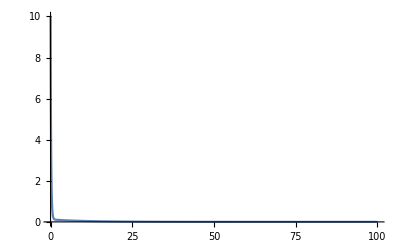
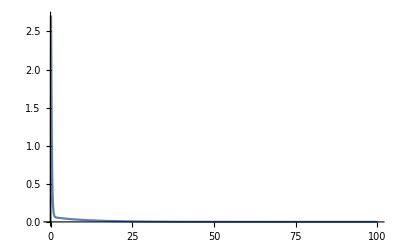
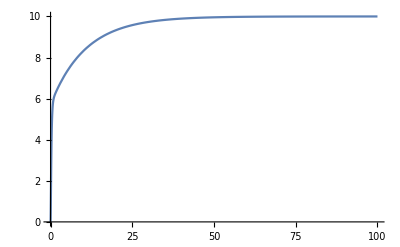
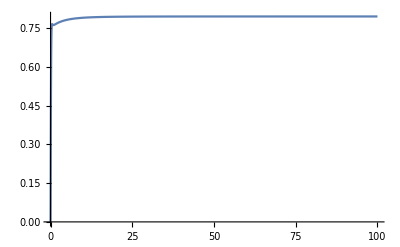
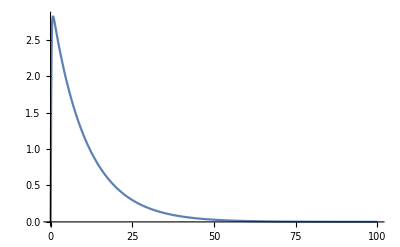
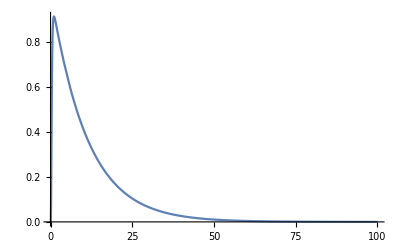
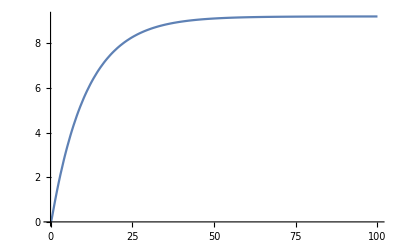

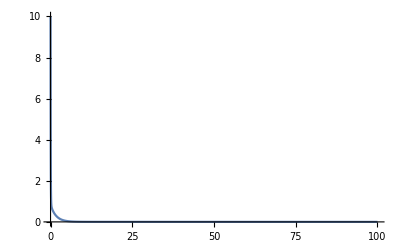

```mathematica
sol =NDSolve[generateExpressions[S[[All,Range[Length[S[[1,All]]]-3]]],species,Join[{10},ConstantArray[0,Length[species]-1]],t,baseLineKs*ratioKs],species,{t,0,1000}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,100},PlotRange -> All]&,species]
```

```mathematica
l = Range[10]
l[[3;;8]]
```

{1,2,3,4,5,6,7,8,9,10}

{3,4,5,6,7,8}